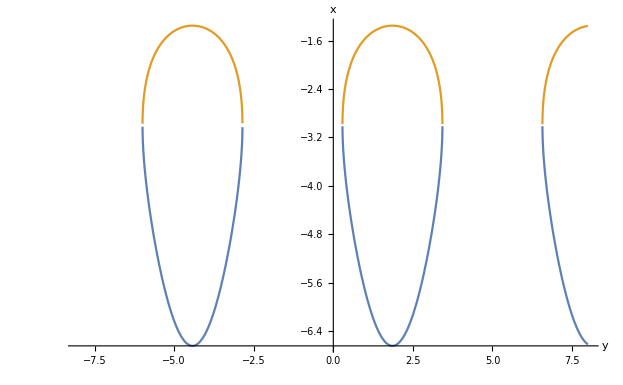

```mathematica
Plot[{Cos[y-5]-3-√((Cos[y-5]-3)^2 -9),Cos[y-5]-3+√((Cos[y-5]-3)^2 -9)},{y,-8,8},AxesLabel->{"y","x"}]
```

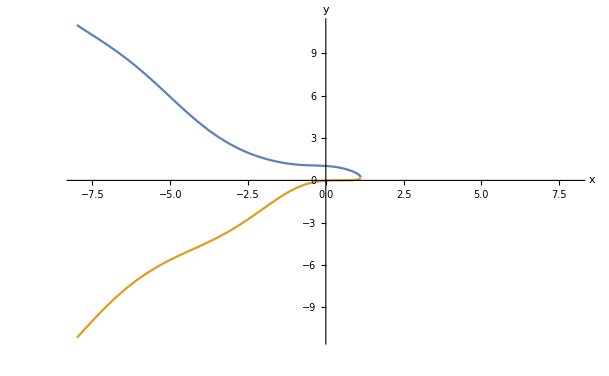

```mathematica
Plot[{0.5*Cos[x] +√((Cos[x]/2)^2 -0.2*(x-0.5)^3),0.5*Cos[x] -√((Cos[x]/2)^2 -0.2*(x-0.5)^3)},{x,-8,8},AxesLabel->{"x","y"}]
```

```mathematica
X[y_]:=Cos[y-5]-3-√((Cos[y-5]-3)^2 -9);
```

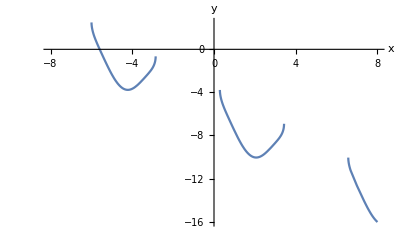

```mathematica
Plot[{0.5*Cos[Cos[y-5]-3-√((Cos[y-5]-3)^2 -9)] -√((Cos[Cos[y-5]-3-√((Cos[y-5]-3)^2 -9)]/2)^2 -0.2*(Cos[y-5]-3-√((Cos[y-5]-3)^2 -9)-0.5)^3) - y},{y,-8,8},AxesLabel->{"x","y"}]
```